```mathematica
Manipulate[Plot3D[Exp[-(2 Sin[π Abs[d1-d2]/ p]^2)/l^2],{d1,-1,1},{d2,-1,1},PlotRange->{0,1}],{{p,.3},0.00001,2},{l,0.00001,10}]
```

```mathematica
Manipulate[ContourPlot[Exp[-(2 Sin[π Abs[d1-d2]/ p]^2)/l^2],{d1,-1,1},{d2,-1,1},PlotLegends->Automatic,PlotRange->{-1,1}],{{p,.3},0.00001,2},{l,0.00001,100}]
```

```mathematica
D[Exp[-(2 Sin[(π dist)/p ]^2)/l^2],l]//FullSimplify

D[Exp[-(2 Sin[(π dist)/p ]^2)/l^2],p]//FullSimplify
```

(4 ⅇ^(-(2 Sin[(dist π)/p]^2)/l^2) Sin[(dist π)/p]^2)/l^3

```mathematica
(2 dist ⅇ^(-(2 Sin[(dist π)/p]^2)/l^2) π Sin[(2 dist π)/p])/(l^2 p^2)
```

Below is the modified  periodic kernel without the “constant”

```mathematica
Manipulate[Plot[(Exp[Cos[2π Abs[d]/ p]/l^2]-BesselI[0,1/l^2])/(Exp[1/l^2]-BesselI[0,1/l^2]),{d,-1,1},PlotRange->{-1,1}],{{p,.3},0.00001,2},{l,0.00001,10}]
```

```mathematica
kernelFn=(Exp[Cos[(2π dists)/p]/l^2]-BesselI[0,1/l^2])/(Exp[1/l^2]-BesselI[0,1/l^2])
FullSimplify[kernelFn]
dKdl=FullSimplify[D[kernelFn,l]]
dKdp=FullSimplify[D[kernelFn,p]]
```

(ⅇ^(Cos[(2 dists π)/p]/l^2)-BesselI[0,1/l^2])/(ⅇ^(1/l^2)-BesselI[0,1/l^2])

(ⅇ^(Cos[(2 dists π)/p]/l^2)-BesselI[0,1/l^2])/(ⅇ^(1/l^2)-BesselI[0,1/l^2])

-((2 ((-ⅇ^(1/l^2)+ⅇ^(Cos[(2 dists π)/p]/l^2)) BesselI[1,1/l^2]+BesselI[0,1/l^2] (ⅇ^(1/l^2)-ⅇ^(Cos[(2 dists π)/p]/l^2) Cos[(2 dists π)/p])-2 ⅇ^((2 Cos[(dists π)/p]^2)/l^2) Sin[(dists π)/p]^2))/(l^3 (ⅇ^(1/l^2)-BesselI[0,1/l^2])^2))

(2 dists ⅇ^(Cos[(2 dists π)/p]/l^2) π Sin[(2 dists π)/p])/(l^2 p^2 (ⅇ^(1/l^2)-BesselI[0,1/l^2]))

```mathematica
Reduce[ⅇ^((2 (Cos[(d π)/p])^2)/l^2)==ⅇ^((1+Cos[2(d π)/p])/l^2)]

ⅇ^(oneOverL2 (1+Cos[PeriodDist]))==ⅇ^oneOverL2 ⅇ^Cos[PeriodDist]
ⅇ^(a (1+b))==ⅇ^a ⅇ^(a b)
```

ⅇ^((2 Cos[(d π)/p]^2)/l^2)==ⅇ^((1+Cos[(2 d π)/p])/l^2)

ⅇ^(oneOverL2 (1+Cos[PeriodDist]))==ⅇ^(oneOverL2+Cos[PeriodDist])

ⅇ^(a (1+b))==ⅇ^(a+a b)

```mathematica
rules = {
1/l^2->oneOverL2,
BesselI[0,oneOverL2]->Bess0,
BesselI[1,oneOverL2]->Bess1,
(dists π)/p->PeriodDist,
(2 dists π)/p->TwoPeriodDist,
Cos[TwoPeriodDist]->Cos2Dist
,Sin[PeriodDist]^2-> 1-Cos[PeriodDist]^2,
(*
Cos[PeriodDist]^2->1/2(1+Cos[PeriodDist])*)
(*
oneOverL2 (1+Cos[PeriodDist])-> oneOverL2 + oneOverL2 Cos[PeriodDist],
ⅇ^(oneOverL2+oneOverL2 Cos[PeriodDist])->ⅇ^oneOverL2 expScaledDists,
ⅇ^(oneOverL2 Cos[2 PeriodDist])->expScaledDists
*)
};
kernelFn//.rules//FullSimplify

dKdlSimple =(( dKdl//.rules)//FullSimplify)//DisplayForm

dKdp//.rules//Simplify
```

(ⅇ^(Cos[(2 dists π)/p]/l^2)-BesselI[0,1/l^2])/(ⅇ^(1/l^2)-BesselI[0,1/l^2])//.{1/l^2→oneOverL2,BesselI[0,oneOverL2]→Bess0,BesselI[1,oneOverL2]→Bess1,(dists π)/p→PeriodDist,(2 dists π)/p→TwoPeriodDist,Cos[TwoPeriodDist]→Cos2Dist,Sin[PeriodDist]^2→Sin[PeriodDist]^2,Null}

-((2 ((-ⅇ^(1/l^2)+ⅇ^(Cos[(2 dists π)/p]/l^2)) BesselI[1,1/l^2]+BesselI[0,1/l^2] (ⅇ^(1/l^2)-ⅇ^(Cos[(2 dists π)/p]/l^2) Cos[(2 dists π)/p])-2 ⅇ^((2 Cos[(dists π)/p]^2)/l^2) Sin[(dists π)/p]^2))/(l^3 (ⅇ^(1/l^2)-BesselI[0,1/l^2])^2))//.{1/l^2→oneOverL2,BesselI[0,oneOverL2]→Bess0,BesselI[1,oneOverL2]→Bess1,(dists π)/p→PeriodDist,(2 dists π)/p→TwoPeriodDist,Cos[TwoPeriodDist]→Cos2Dist,Sin[PeriodDist]^2→Sin[PeriodDist]^2,Null}

(2 dists ⅇ^(Cos[(2 dists π)/p]/l^2) π Sin[(2 dists π)/p])/(l^2 p^2 (ⅇ^(1/l^2)-BesselI[0,1/l^2]))//.{1/l^2→oneOverL2,BesselI[0,oneOverL2]→Bess0,BesselI[1,oneOverL2]→Bess1,(dists π)/p→PeriodDist,(2 dists π)/p→TwoPeriodDist,Cos[TwoPeriodDist]→Cos2Dist,Sin[PeriodDist]^2→Sin[PeriodDist]^2,Null}

```mathematica
Numerator[dKdl]//FullSimplify
```

2 (ⅇ^(1/l^2)-ⅇ^(Cos[(2 dists π)/p]/l^2)) BesselI[1,1/l^2]-2 BesselI[0,1/l^2] (ⅇ^(1/l^2)-ⅇ^(Cos[(2 dists π)/p]/l^2) Cos[(2 dists π)/p])+4 ⅇ^((2 Cos[(dists π)/p]^2)/l^2) Sin[(dists π)/p]^2

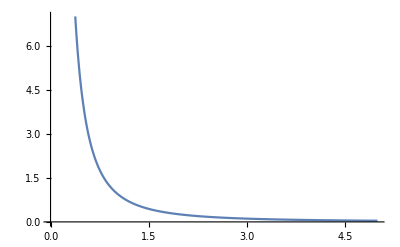

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

```mathematica
Plot[1/l^2,{l,0.01,5},PlotRange->{0,7}]
Reduce[1/l^2<3.75 && l>0,Reals]
```

```mathematica
l>0.5163977794943222
```

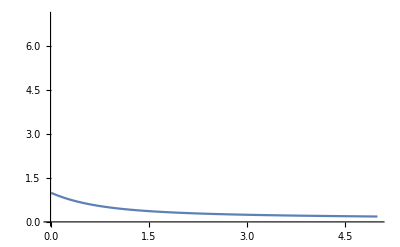

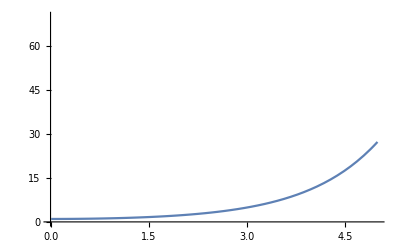

```mathematica
Plot[BesselI[0,l]Exp[-l],{l,0.01,5},PlotRange->{0,7}]
Plot[BesselI[0,l],{l,0.01,5},PlotRange->{0,70}]
```

```mathematica
Reduce[ⅇ^(-2/l^2+Cos[(2 dists π)/p]/l^2)BesselI[0,1/l^2]== ⅇ^(-1/l^2)*ⅇ^(-1/l^2)* ⅇ^(Cos[(2 dists π)/p]/l^2)BesselI[0,1/l^2]]

 Reduce[ⅇ^(-1/l^2)*ⅇ^(-1/l^2)* ⅇ^(Cos[(2 dists π)/p]/l^2)BesselI[0,1/l^2] == ⅇ^(-1/l^2)*BesselI[0,1/l^2]*ⅇ^(-1/l^2)* ⅇ^(Cos[(2 dists π)/p]/l^2)]

 Reduce[ⅇ^(-1/l^2)*ⅇ^(-1/l^2)* ⅇ^(Cos[(2 dists π)/p]/l^2)BesselI[0,1/l^2] == expBess0*ⅇ^(-1/l^2)* ⅇ^(Cos[(2 dists π)/p]/l^2)
&& ⅇ^(-1/l^2)*BesselI[0,1/l^2] == expBess0
&& expBess0≠ 0 && BesselI[0,1/l^2]≠0
]


rules = {
ⅇ^(-2/l^2+Cos[(2 dists π)/p]/l^2)->  ⅇ^(-1/l^2)*ⅇ^(-1/l^2)* ⅇ^(Cos[(2 dists π)/p]/l^2),
 ⅇ^(-2/l^2+Cos[(2 dists π)/p]/l^2) BesselI[0,1/l^2]->  expBess0*ⅇ^(-1/l^2)* ⅇ^(Cos[(2 dists π)/p]/l^2),
ⅇ^(-2/l^2+Cos[(2 dists π)/p]/l^2) BesselI[1,1/l^2]->  expBess1*ⅇ^(-1/l^2)* ⅇ^(Cos[(2 dists π)/p]/l^2),
ⅇ^(-1/l^2) BesselI[1,1/l^2]-> expBess1,
ⅇ^(-1/l^2) BesselI[0,1/l^2]-> expBess0,
Sin[x_]^2-> 1-Cos[x]^2
};
(((Numerator[dKdl]*Exp[-2/l^2])//Expand )//.rules  ) //FullSimplify
```

True

True

expBess0≠0&&ⅇ^(1/l^2)==BesselI[0,1/l^2]/expBess0&&BesselI[0,1/l^2]≠0

2 (-expBess0+expBess1+ⅇ^(-(2 Sin[(dists π)/p]^2)/l^2) (1-expBess1+(-1+expBess0) Cos[(2 dists π)/p]))

```mathematica
Reduce[ⅇ^(-2/l^2) BesselI[0,1/l^2]^2== (ⅇ^(-1/l^2) BesselI[0,1/l^2])^2]
rules = {
 
ⅇ^(-2/l^2) BesselI[0,1/l^2]^2->  (expBess0)^2,

ⅇ^(-1/l^2) BesselI[0,1/l^2]-> expBess0
};
((Denominator[dKdl]*Exp[-2/l^2]/l^3//Expand)//.rules)*l^3 //FullSimplify
```

```mathematica
True
```

(-1+expBess0)^2 l^3

```mathematica
matrixEntry[i_,j_] = If[i<j,
Symbol["dist"<>TextString[i]<>TextString[j]],
Symbol["dist"<>TextString[j]<>TextString[i]]
];

D[Table[(Exp[Cos[(2π matrixEntry[i,j])/p]/l^2]-BesselI[0,1/l^2])/(Exp[1/l^2]-BesselI[0,1/l^2]),{i,1,3},{j,1,3}],p]//MatrixForm//Simplify
```

((2 dist11 ⅇ^(Cos[(2 dist11 π)/p]/l^2) π Sin[(2 dist11 π)/p])/(l^2 p^2 (ⅇ^(1/l^2)-BesselI[0,1/l^2])) | (2 dist12 ⅇ^(Cos[(2 dist12 π)/p]/l^2) π Sin[(2 dist12 π)/p])/(l^2 p^2 (ⅇ^(1/l^2)-BesselI[0,1/l^2])) | (2 dist13 ⅇ^(Cos[(2 dist13 π)/p]/l^2) π Sin[(2 dist13 π)/p])/(l^2 p^2 (ⅇ^(1/l^2)-BesselI[0,1/l^2]))
(2 dist12 ⅇ^(Cos[(2 dist12 π)/p]/l^2) π Sin[(2 dist12 π)/p])/(l^2 p^2 (ⅇ^(1/l^2)-BesselI[0,1/l^2])) | (2 dist22 ⅇ^(Cos[(2 dist22 π)/p]/l^2) π Sin[(2 dist22 π)/p])/(l^2 p^2 (ⅇ^(1/l^2)-BesselI[0,1/l^2])) | (2 dist23 ⅇ^(Cos[(2 dist23 π)/p]/l^2) π Sin[(2 dist23 π)/p])/(l^2 p^2 (ⅇ^(1/l^2)-BesselI[0,1/l^2]))
(2 dist13 ⅇ^(Cos[(2 dist13 π)/p]/l^2) π Sin[(2 dist13 π)/p])/(l^2 p^2 (ⅇ^(1/l^2)-BesselI[0,1/l^2])) | (2 dist23 ⅇ^(Cos[(2 dist23 π)/p]/l^2) π Sin[(2 dist23 π)/p])/(l^2 p^2 (ⅇ^(1/l^2)-BesselI[0,1/l^2])) | (2 dist33 ⅇ^(Cos[(2 dist33 π)/p]/l^2) π Sin[(2 dist33 π)/p])/(l^2 p^2 (ⅇ^(1/l^2)-BesselI[0,1/l^2])))

```mathematica
({{(2 dist11 ⅇ^(Cos[(2 dist11 π)/p]/l^2) π Sin[(2 dist11 π)/p])/(l^2 p^2 (ⅇ^(1/l^2)-BesselI[0,1/l^2])), (2 dist12 ⅇ^(Cos[(2 dist12 π)/p]/l^2) π Sin[(2 dist12 π)/p])/(l^2 p^2 (ⅇ^(1/l^2)-BesselI[0,1/l^2])), (2 dist13 ⅇ^(Cos[(2 dist13 π)/p]/l^2) π Sin[(2 dist13 π)/p])/(l^2 p^2 (ⅇ^(1/l^2)-BesselI[0,1/l^2]))}, {(2 dist12 ⅇ^(Cos[(2 dist12 π)/p]/l^2) π Sin[(2 dist12 π)/p])/(l^2 p^2 (ⅇ^(1/l^2)-BesselI[0,1/l^2])), (2 dist22 ⅇ^(Cos[(2 dist22 π)/p]/l^2) π Sin[(2 dist22 π)/p])/(l^2 p^2 (ⅇ^(1/l^2)-BesselI[0,1/l^2])), (2 dist23 ⅇ^(Cos[(2 dist23 π)/p]/l^2) π Sin[(2 dist23 π)/p])/(l^2 p^2 (ⅇ^(1/l^2)-BesselI[0,1/l^2]))}, {(2 dist13 ⅇ^(Cos[(2 dist13 π)/p]/l^2) π Sin[(2 dist13 π)/p])/(l^2 p^2 (ⅇ^(1/l^2)-BesselI[0,1/l^2])), (2 dist23 ⅇ^(Cos[(2 dist23 π)/p]/l^2) π Sin[(2 dist23 π)/p])/(l^2 p^2 (ⅇ^(1/l^2)-BesselI[0,1/l^2])), (2 dist33 ⅇ^(Cos[(2 dist33 π)/p]/l^2) π Sin[(2 dist33 π)/p])/(l^2 p^2 (ⅇ^(1/l^2)-BesselI[0,1/l^2]))}})
```